```mathematica
(*Avtomatsko shranjevanje notebook-a*)
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

# Vaje za 3. teden

5.  3.  2026

## Naloga 1

V pomoči si poglej ukaz Join. Definiraj seznam {1,2,...,100,1,2,...,100}. Definiraj še funkcijo DvojniSeznam[n], ki vrne dvojni seznam {1,2,...,n,1,2,...,n}.

```mathematica
Join[{Range[100]},{Range[100]}];
DvojniSeznam[n_]:=Join[Range[n],Range[n]]
```

Kaj dela spodnja funkcija?

```mathematica
Krogi[n_]:=Join[{Red},Table[Disk[{2i,0}],{i,n}]]
```

```mathematica
t = Krogi[3]
```

```mathematica
{RGBColor[1, 0, 0],Disk[{2,0}],Disk[{4,0}],Disk[{6,0}]}
```

Krogi naredi seznam rdeče barve in treh krogov polmera 1

Definiraj funkcijo NarisiKroge[n], ki nariše n rdečih krogov. Barve lahko definiraš tudi drugače, uporabi domišljijo. Pomagaj si s funkcijo Graphics. Na primer, klic NarisiKroge[5] naj vrne nekaj takega kot:

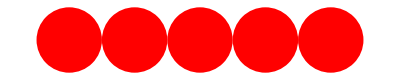

```mathematica
NarisiKroge[n_]:=Graphics[Krogi[n]]
```

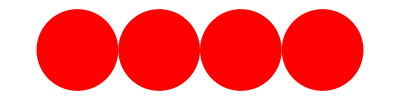

```mathematica
NarisiKroge[4]
```

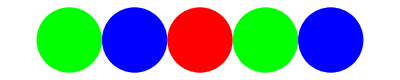
Za dodatni izziv poskusi napisati funkcijo MesaniKrogi[n], ki bo narisala kroge v izmenjajočih barvah. Na primer:
-Graphics-

Na podoben način definiraj še funkcijo NarisiKrogle[n], ki nariše n sfer . Sfere lahko postaviš tudi drugače (ne nujno v ravni vrsti) .

```mathematica
Krogle[n_]:=Join[{Green},Table[Sphere[{0,2i,0}],{i,n}]]
```

```mathematica
NarisiKrogle[n_]:= Graphics3D[Krogle[n]]
```

```mathematica
NarisiKrogle[100]
```

-Graphics3D-

```mathematica
(*mešane barve*)
```

```mathematica
barve = {{Red},{Green},{Blue}}
MesaniKrogi[n_]:= Flatten[Join[Flatten[Table[{{Red},{Green},{Blue}},Ceiling[n/3]], 1], Table[{Disk[{2i,0}]},{i,n}],2]]
```

{{RGBColor[1, 0, 0]},{RGBColor[0, 1, 0]},{RGBColor[0, 0, 1]}}

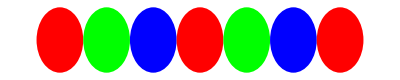

```mathematica
Graphics[MesaniKrogi[7]]
```

Nariši interaktivni 3d graf, ki vsebuje tri zaporedne krogle, vsaki od katerih lahko spreminjaš njeno drugo koordinato.

-Graphics3D-

```mathematica
Manipulate[Graphics3D[               {Sphere[{0,y1,0}],Sphere[{0,y2,0}],Sphere[{0,y3,0}]}]              ,                      {{y1,2},0,10},{y2,0,10},{{y3,6},0,10}]
```

## Naloga 2

Napiši funkcijo, ki sprejme naravni števili m in n in vrne seznam prvih n členov Collatzovega zaporedja za število m. Pomagaj si s funkcijo “RecurrenceTable”.

```mathematica
Collatz[m_]:=If[Mod[m,2]==0,m/2,3 m+1]
```

```mathematica
Collatz[7]
```

22

```mathematica
(*fibonaci za test*)
```

```mathematica
RecurrenceTable[
{a[n]==a[n-1]+a[n-2],
a[1]==1,a[2]==1}

,a, 
  {n,10}]
```

{1,1,2,3,5,8,13,21,34,55}

```mathematica
ClearAll[a]
```

```mathematica
CollZap[m_,n_]:=RecurrenceTable[
{a[k]==If[EvenQ[a[k-1]],a[k-1]/2,3 *a[k-1]+1],
a[1]==m}

,a,
{k,1,n}]
```

```mathematica
CollZap[7,5] (*!!!!!!!!!! Zakaj ni prav?*)
```

{7,22,67,202,607}

```mathematica
EvenQ[22]
```

True

## Naloga 3

Napiši  funkcijo quickSort, ki sprejme seznam in vrne urejen seznam. Za urejanje naj uporabi algoritem Quick sort.

```mathematica
Clear[quickSort];
quickSort[list_List]:=If[Length[list]<=1,list,Module[{pivot,rest,left,right},pivot=First[list];
rest=Rest[list];
left=Select[rest,#<=pivot&];
right=Select[rest,#>pivot&];
Join[quickSort[left],{pivot},quickSort[right]]]]
```

```mathematica
quickSort[{3,1,4,1,5,9,2}]
(*Rezultat:{1,1,2,3,4,5,9}*)
```

{1,1,2,3,4,5,9}

## Naloga 4

Napiši funkcijo odvod polinoma, ki kot argument sprejme polinom v splošni obliki in vrne njegov odvod. Pri tem uporabi le prepisovalna pravila.